1. Интеграл Фурье

(2 Sin[l/2]^2)/l^2

0

ConditionalExpression[-1/2 π (-1+t),0<Re[t]<1&&Im[t]==0]

2. Интеграл Фурье продолженной функции

ConditionalExpression[1/16 ⅇ^(-ⅈ t) ((4 (1+ⅇ^(2 ⅈ t)) Abs[π-t])/(π-t)+(4 (1+ⅇ^(2 ⅈ t)) Abs[π+t])/(π+t)+1/π(-π-2 ⅇ^(2 ⅈ t) π+4 ⅈ (-1+ⅇ^(2 ⅈ t)) CosIntegral[2 (π-t)]+4 ⅈ (-1+ⅇ^(2 ⅈ t)) CosIntegral[-2 (π+t)]+4 ⅈ CosIntegral[2 (π+t)]-4 ⅈ ⅇ^(2 ⅈ t) CosIntegral[2 (π+t)]+4 ⅈ CosIntegral[-2 π+2 t]-4 ⅈ ⅇ^(2 ⅈ t) CosIntegral[-2 π+2 t]-2 ⅈ Log[2]+2 ⅈ Log[-π-t]-4 ⅈ ⅇ^(2 ⅈ t) Log[-π-t]-2 ⅈ Log[-ⅈ/(π-t)]+2 ⅈ Log[ⅈ/(π-t)]+2 ⅈ Log[-ⅈ (π-t)]+2 ⅈ ⅇ^(2 ⅈ t) Log[ⅈ (π-t)]+2 ⅈ Log[-4 ⅈ (π-t)]+4 ⅈ Log[π-t]-4 ⅈ ⅇ^(2 ⅈ t) Log[π-t]-2 ⅈ Log[(π-t)^2]-4 ⅈ Log[-π+t]+2 ⅈ ⅇ^(2 ⅈ t) Log[-π+t]+2 ⅈ Log[-ⅈ/(2 (π+t))]-2 ⅈ Log[-ⅈ/(π+t)]+2 ⅈ ⅇ^(2 ⅈ t) Log[-ⅈ (π+t)]+2 ⅈ Log[ⅈ (π+t)]-4 ⅈ Log[π+t]+2 ⅈ ⅇ^(2 ⅈ t) Log[π+t])),t∈ℝ]

ConditionalExpression[1/2 (-Cos[(π-t)/Sign[π-t]] Sign[π-t]+Cos[t] Sign[t]),t∈ℝ]

3. Синус и косинус преобразования Фурье

1/2 √3 (Cos[(3 l^2)/4] FresnelC[(10-3 l)/(√(6 π))]+Cos[(3 l^2)/4] FresnelC[(10+3 l)/(√(6 π))]+(FresnelS[(10-3 l)/(√(6 π))]+FresnelS[(10+3 l)/(√(6 π))]) Sin[(3 l^2)/4])

1/2 √3 (-2 Cos[(3 l^2)/4] FresnelS[l √(3/(2 π))]-Cos[(3 l^2)/4] FresnelS[(10-3 l)/(√(6 π))]+Cos[(3 l^2)/4] FresnelS[(10+3 l)/(√(6 π))]+2 FresnelC[l √(3/(2 π))] Sin[(3 l^2)/4]+FresnelC[(10-3 l)/(√(6 π))] Sin[(3 l^2)/4]-FresnelC[(10+3 l)/(√(6 π))] Sin[(3 l^2)/4])

4. Прямое и обратное преобразования Фурье

Piecewise[{{Cos[t^2/3], 0≤t≤5}, {0, True}}]

Из-за мнимой единицы, график не отображается.

-(((1/8-ⅈ/8) √3 (Cos[(3 l^2)/4]-ⅈ Sin[(3 l^2)/4]) (-l Abs[10-3 l] Abs[10+3 l] Cos[(3 l^2)/2] Erf[(1/2+ⅈ/2) √(3/2) Abs[l]]+l Abs[10-3 l] Abs[10+3 l] Erfi[(1/2+ⅈ/2) √(3/2) Abs[l]]+Abs[l] (-(10+3 l) Abs[10-3 l] Erfi[((1/2+ⅈ/2) Abs[10+3 l])/(√6)]+(-10+3 l) Abs[10+3 l] Erf[((1/2+ⅈ/2) Abs[10-3 l])/(√6)] (Cos[(3 l^2)/2]+ⅈ Sin[(3 l^2)/2]))-ⅈ l Abs[10-3 l] Abs[10+3 l] Erf[(1/2+ⅈ/2) √(3/2) Abs[l]] Sin[(3 l^2)/2]))/(Abs[10-3 l] Abs[l] Abs[10+3 l]))

InverseFourierTransform[(1/8-ⅈ/8) √3 (Cos[(3 l^2)/4]-ⅈ Sin[(3 l^2)/4]) (Cos[(3 l^2)/2] Erf[(5+5 ⅈ)/(√6)-(1/2+ⅈ/2) √(3/2) l]+Cos[(3 l^2)/2] Erf[l Root0.612+0.612 ⅈRoot[9+16 #1^4&,4]0.6123724356957945]+Erfi[(5+5 ⅈ)/(√6)+(1/2+ⅈ/2) √(3/2) l]-Erfi[l Root0.612+0.612 ⅈRoot[9+16 #1^4&,4]0.6123724356957945]+ⅈ Erf[(5+5 ⅈ)/(√6)-(1/2+ⅈ/2) √(3/2) l] Sin[(3 l^2)/2]+ⅈ Erf[l Root0.612+0.612 ⅈRoot[9+16 #1^4&,4]0.6123724356957945] Sin[(3 l^2)/2]),l,t]

Обратное преобразование совпадает с исходной функцией.

5. Свёртка функций f и g

Piecewise[{{1, -1<τ≤1}, {1/2 (1-2 τ-τ^2), -2<τ≤-1}, {1/2+τ-τ^2/2, 1<τ<2}, {1/2 (-3+τ)^2, 2≤τ<3}, {1/2 (3+τ)^2, -3<τ≤-2}, {0, True}}]

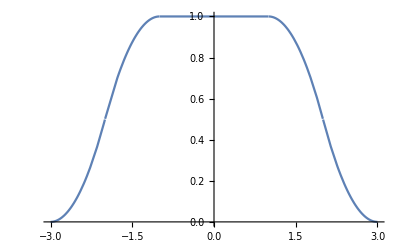

```mathematica
Clear[f,a,b,f2]
Style[Text["1. Интеграл Фурье"],FontSize->16]
f[t_]:=Piecewise[{
{(Pi(1-Abs[t])/2),Abs[t]≤ 1},
{0, Abs[t]>1}}
];
a[l_]=1/Pi*Integrate[f[τ]*Cos[l*τ],{τ,-Infinity,Infinity}]
b[l_]=1/Pi*Integrate[f[τ]*Sin[l*τ],{τ,-Infinity,Infinity}]
g[t_]=Integrate[a[l]*Cos[l*t],{l,0,Infinity}]+
Integrate[b[l]*Sin[l*t],{l,0,Infinity}]
Style[Text["2. Интеграл Фурье продолженной функции"],FontSize->16]
f2[t_]:=Piecewise[{
{Cos[t], 0≤t≤Pi},
{0, t>Pi}}
];
f2Sym[t_]:=Piecewise[{
{f2[t], 0≤t<Infinity}, 
{f2[-t], -Infinity≤t<0}}
];
f2Asym[t_]:=Piecewise[{
{f2[t], 0≤t<Infinity}, 
{-f2[t], -Infinity≤t<0}}
];
coeffs2Sym[λ_]:=1/(2 Pi) Integrate[f2Sym[τ]  Exp[-I λ τ], {τ, -Infinity, Infinity},Assumptions->λ  ∈ Reals]
coeffs2Asym[λ_]:=1/(2 Pi) Integrate[f2Asym[τ]  Exp[-I λ τ], {τ, -Infinity, Infinity},Assumptions->λ  ∈ Reals]
IntFourierSym[t_]:=Integrate[coeffs2Sym[λ] Exp[I λ t], {λ, -Infinity, Infinity}]
IntFourierAsym[t_]:=Integrate[coeffs2Asym[λ] Exp[I λ t], {λ, -Infinity, Infinity}]
IntFourierSym[t]
IntFourierAsym[t]
Style[Text["3. Синус и косинус преобразования Фурье"],FontSize->16]
f[t_]:=Piecewise[{
{Cos[t^2/3],0≤t≤5},
{0,t>5}}
];
FourierCosTransform[f[t],t,l]
FourierSinTransform[f[t],t,l]
Style[Text["4. Прямое и обратное преобразования Фурье"],FontSize->16]
f[t_,λ_]:=E^(-t^2/2)*E^(I*λ*t)//Simplify
f[t]
Manipulate[Plot[f[t,λ],{t,-3,3}],{λ,-4,4}]
Style[Text["Из-за мнимой единицы, график не отображается."],FontSize->13]
FourierTransform[f[t],t,l]
g[l_]:=FourierTransform[f[t],t,l]
InverseFourierTransform[g[l],l,t]
Style[Text["Обратное преобразование совпадает с исходной функцией."],FontSize->16]
Style[Text["5. Свёртка функций f и g"],FontSize->16]
f[t_]:=Piecewise[{
{1-Abs[t],Abs[t]< 1},
{0,Abs[t]≥ 1}}
];
g[t_]:=Piecewise[{
{1,Abs[t]< 2},
{0,Abs[t]≥ 2}}
];
Convolve[f[t],g[t],t,τ]
Plot[Convolve[f[t],g[t],t,τ],{τ,-3,3}]
```